# Some MPM Meshes

Remarks: Output requires node ID starting by 0!

```mathematica
OutputDirectory=ParentDirectory[NotebookDirectory[]]<>"/data/";
```

```mathematica
ParticleX2D[toelementmesh_]:=Module[
{MeshElements,MeshCoord,NoElements,PX,PV},
MeshCoord=toelementmesh["Coordinates"];
MeshElements=toelementmesh["MeshElements"]⟦1,1⟧;
NoElements=Length[MeshElements];
Return[Table[
(*Compute Particle Position PX (element center)*)
PX=Mean[MeshCoord⟦MeshElements⟦i⟧⟧];
(*Compute Particle Position PX (element center)*)
PV=Area[Polygon[MeshCoord⟦MeshElements⟦i⟧⟧]];
(*Output as 3d coordinates followed by volume*)
{PX⟦1⟧,PX⟦2⟧,0.0,PV}
,{i,NoElements}]]
]
```

#### Rectangular Q4-Grid

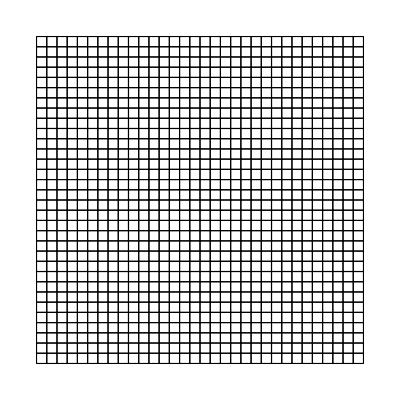

```mathematica
<<NDSolve`FEM`;
GridMesh=ToElementMesh[
Rectangle[{0,0},{1,1}]
,"MeshOrder"->1
,MaxCellMeasure->0.001
];
GridMesh["Wireframe"]
Node=GridMesh["Coordinates"];
ElementConnectivity=GridMesh["MeshElements"]⟦1,1⟧-1;
```

#### Falling Bar

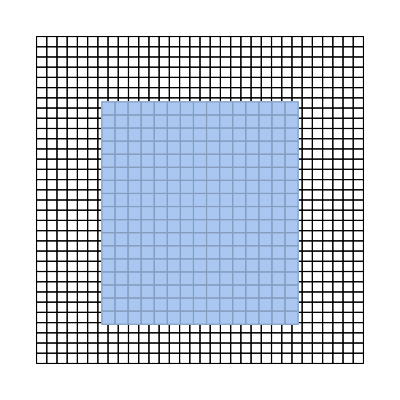

```mathematica
<<NDSolve`FEM`;
GridMesh=ToElementMesh[
Rectangle[{0,0},{1,1}]
,"MeshOrder"->1
,MaxCellMeasure->0.001
];
BarMesh=ToElementMesh[
Rectangle[{0.2,0.12},{0.8,0.8}]
,"MeshOrder"->1
,MaxCellMeasure->0.0018
];
Show[
GridMesh["Wireframe"],MeshRegion[BarMesh]]
```

```mathematica
Node=GridMesh["Coordinates"];
ElementConnectivity=GridMesh["MeshElements"]⟦1,1⟧-1;

Export[OutputDirectory<>"/falling_bar_node.txt",Node,"CSV"]
Export[OutputDirectory<>"/falling_bar_element.txt",ElementConnectivity,"CSV"]
```

/Users/sash/mpm_2d/data//falling_bar_node.txt

/Users/sash/mpm_2d/data//falling_bar_element.txt

```mathematica
Export[
OutputDirectory<>"/falling_bar_particle.txt",
ParticleX2D[BarMesh],
"CSV"]
```

/Users/sash/mpm_2d/data//falling_bar_particle.txt

# A MPM Mesh ToolFrame

## Functions

```mathematica
(*Return "internal points" of a given quadrilateral with volume*)
GP4[XI_]:=Module[{SHP,ξ,η,X,a,A},
SHP=1/4{(1-ξ)(1-η),(1+ξ)(1-η),(1+ξ) (1+η),(1-ξ) (1+η)};
X=SHP.XI;
a=0.5;Sqrt[1/3];
A=Area[Polygon[XI]]/4;
Return[N[{{X/.{ξ->-a,η->-a},X/.{ξ->a,η->-a},X/.{ξ->a,η->a},X/.{ξ->-a,η->a}},{A,A,A,A}}]];
];

(*A regular Grid generator*)
RegularGrid[w_,h_,dx_]:=Module[{XI,NElmtX,NElmtY,Elmt},
XI=Partition[Flatten[Table[{i,j},{j,0,h,dx},{i,0,w,dx}]],2];
{NElmtX,NElmtY}=IntegerPart[{w/dx,h/dx}];
Elmt=Partition[Flatten[Table[{
(j-1)(NElmtX+1)+(i-1)+1
,(j-1)(NElmtX+1)+(i-1)+2
,j(NElmtX+1)+(i-1)+2
,j(NElmtX+1)+(i-1)+1
}
,{i,NElmtX},{j,NElmtY}]],4];
Return[{XI,Elmt}];
];
```

```mathematica
(*Return list of pointsnumbers inside region Reg*)
RegionParticles[XI_,Reg_]:=Module[{},
Return[
Select[XI,RegionMember[Reg]]
];
];
```

## Metal Cutting

```mathematica
(*define bodys as regions*)
Piece=Rectangle[{0,0},{1.0,0.6}];
Tool=Rectangle[{1.1,0.5},{1.3,0.8}];
(*define mesh density and generate mesh*)
{w,h,dx}={1.4,1.0,.05};
{XI,Elmt}=RegularGrid[w,h,dx];
(*get all mesh subpoints and volumes(volumes are equal in regular grid)*)
GPI=Partition[Flatten[Map[GP4[XI⟦#⟧]&,Elmt]⟦All,1⟧],2];
VI=GP4[XI⟦Elmt⟦1⟧⟧]⟦2,1⟧;
(*generate sublists with points inside bodies*)
PTPiece=RegionParticles[GPI,Piece];
PTTool=RegionParticles[GPI,Tool];
```

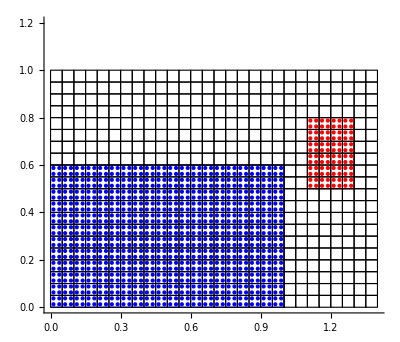

```mathematica
Graphics[{
{EdgeForm[{Blue}],FaceForm[None],Piece}
,{EdgeForm[{Red}],FaceForm[None],Tool}
,GraphicsComplex[XI,{FaceForm[None],EdgeForm[Thin],Polygon[Elmt]}]
,{Blue,Point[PTPiece]}
,{Red,Point[PTTool]}
}
,PlotRange->{{0,1.4},{0,1.2}}
,Axes->True
]
```

```mathematica
(*Write Grid Files !index starting 0*)
OutputDirectory=ParentDirectory[NotebookDirectory[]]<>"/metal_cut/";
Export[
OutputDirectory<>"/Nodes.cvs",
Map[Append[#,0]&,XI],
"CSV"]
Export[
OutputDirectory<>"/Elements.cvs",
Elmt-1,
"CSV"]
Export[
OutputDirectory<>"/Tool.cvs",
Map[Append[Append[#,0],VI]&,PTTool],
"CSV"]
Export[
OutputDirectory<>"/Piece.cvs",
Map[Append[Append[#,0],VI]&,PTPiece],
"CSV"]
```

/Users/sash/mpm_2d/metal_cut//Nodes.cvs

/Users/sash/mpm_2d/metal_cut//Elements.cvs

/Users/sash/mpm_2d/metal_cut//Tool.cvs

/Users/sash/mpm_2d/metal_cut//Piece.cvs

## High Velocity Impact

```mathematica
(*define bodys as regions*)
Impactor=Disk[{30,50},9.53/2];
Target=Rectangle[{0,0},{60,40}];
(*define mesh density and generate mesh*)
{w,h,dx}={60,60,6/5};
{XI,Elmt}=RegularGrid[w,h,dx];
(*get all mesh subpoints and volumes(volumes are equal in regular grid)*)
GPI=Partition[Flatten[Map[GP4[XI⟦#⟧]&,Elmt]⟦All,1⟧],2];
VI=GP4[XI⟦Elmt⟦1⟧⟧]⟦2,1⟧;
(*generate sublists with points inside bodies*)
PTImpactor=RegionParticles[GPI,Impactor];
PTTarget=RegionParticles[GPI,Target];
```

```mathematica
Elmt//Length
PTTarget//Length
PTImpactor//Length
```

2500

6700

196

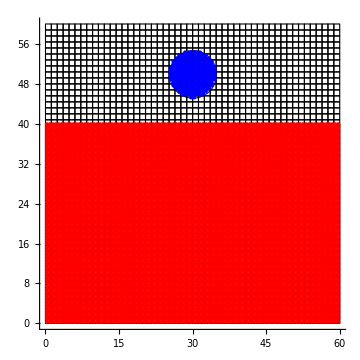

```mathematica
Graphics[{
{EdgeForm[{Blue}],FaceForm[None],Impactor}
,{EdgeForm[{Red}],FaceForm[None],Target}
,GraphicsComplex[XI,{FaceForm[None],EdgeForm[Thin],Polygon[Elmt]}]
,{Blue,Point[PTImpactor]}
,{Red,Point[PTTarget]}
}
,PlotRange->{{0,60},{0,60}}
,Axes->True
,ImageSize->Medium
]
```

```mathematica
(*Write Grid Files !index starting 0*)
OutputDirectory=ParentDirectory[NotebookDirectory[]]<>"/impact/";
Export[
OutputDirectory<>"/Nodes.cvs",
Map[Append[#,0]&,XI],
"CSV"]
Export[
OutputDirectory<>"/Elements.cvs",
Elmt-1,
"CSV"]
Export[
OutputDirectory<>"/Impactor.cvs",
Map[Append[Append[#,0],VI]&,PTImpactor],
"CSV"]
Export[
OutputDirectory<>"/Target.cvs",
Map[Append[Append[#,0],VI]&,PTTarget],
"CSV"]
```

Export::nodir: Directory /Users/sash/mpm_2d/impact/ does not exist.

OpenWrite::noopen: Cannot open /Users/sash/mpm_2d/impact//Nodes.cvs.

$Failed

Export::nodir: Directory /Users/sash/mpm_2d/impact/ does not exist.

OpenWrite::noopen: Cannot open /Users/sash/mpm_2d/impact//Elements.cvs.

$Failed

Export::nodir: Directory /Users/sash/mpm_2d/impact/ does not exist.

OpenWrite::noopen: Cannot open /Users/sash/mpm_2d/impact//Impactor.cvs.

$Failed

Export::nodir: Directory /Users/sash/mpm_2d/impact/ does not exist.

OpenWrite::noopen: Cannot open /Users/sash/mpm_2d/impact//Target.cvs.

$Failed